```mathematica
(*RStarConstValues = {-5,-10,-15,-20,-25,-30,-35};
*)
ExportPath="RStarConst_comparison";
RStarConstValues = {-20,-25,-30,-35};
(*RStarConstValues = {-(2+1/2),-(7+1/2)};*)
For[iteration=1,iteration<=Length[RStarConstValues],iteration+=1,
RStarConst =RStarConstValues[[iteration]];
skip=20;
du=dv=1/100;
massReduct=1/1000;
v1= 0;
m0=1;
Q0=8/10;
SourcesRParam = 1;
SourcesRParamR = 1;
SourcesSParam = 1;
SourcesSParamR =1;
SourcesS5Param = 0;
deltaUV5Param = 70;
QuvFactor =1;
Qreduct=Q0/m0*massReduct;
deltav =900;
v2 =v1+deltav;
Vvec = Table[v,{v,v1,v2,dv}];
MFunc = (m0^3-(v-v1)*massReduct)^(1/3);
QFunc = MFunc * Q0;
Clear[pdesolskip,RTable,STable,RvTable,RvvTable,RuTable,RuuTable,SvTable,SvvTable,SuTable,SuuTable];
Uvec = 2*RStarConst- Vvec;
Uvec0=Table[u,{u,Uvec[[-1]],Uvec[[1]],du}];
UvecSkipped = Uvec0[[1;;-1;;skip]];
VvecSkipped = Vvec[[1;;-1;;skip]];
deltaUV5 = (Uvec0[[1]]+Vvec[[1]])/2+deltaUV5Param; 
vsol=DSolve[{H'[v]==κp/.{Q->QFunc,m->MFunc},H[0]==0},H[v],{v,v1,v2}(*,Method->"StiffnessSwitching",WorkingPrecision->60*)];
vtilde=(H[v]/.vsol/.{v->Vvec})[[1]];
usol=DSolve[{H'[u]==κp/.{Q->(QFunc/.v->-u),m->(MFunc/.v->-u)},H[0]==0},H[u],u(*,{u,Uvec[[1]],Uvec[[-1]]},Method->"StiffnessSwitching",WorkingPrecision->60*)];
utilde=(H[u]/.usol/.{u->Uvec})[[1]];
Ttilde=(utilde+vtilde)/2;
MTable= MFunc/.{v->Vvec}//N100;
QTable = QFunc/.{v->Vvec}//N100;
QuvTable = QuvFactor *massReduct* MTable^-1 ;
QuvScale=MTable^-1;
MuTable = MFunc /. {v->-Uvec}//N100;
QuTable = QFunc /. {v->-Uvec}//N100;
κpu=(κp/.{m->μ,Q->Qu});
sInitFixed = Log[-r *f/2]+Log[κpu]-Log[κp];
DRDUFixed=r f *κpu/κp;
DLogκpuDu=D[Log[κpu],μ]*D[(MFunc/.v->-u),u]+D[Log[κpu],Qu]*D[(QFunc/.v->-u),u];
DSDUFixed=D[Log[-r f ],r] *DRDUFixed/(2r)+DLogκpuDu;
SourcesR=massReduct*SourcesRParam/MTable^3;
SourcesS = massReduct*SourcesSParam/MTable^5;
SourcesRR =massReduct* SourcesRParamR/MTable^4;
SourcesRS = massReduct*SourcesSParamR/MTable^6;
SourcesR5=0*Vvec;
SourcesS5 = massReduct*SourcesS5Param*MTable;
time0=AbsoluteTiming[
RStarVector=Table[ (Ttilde[[j]]/κp/.{m->MTable[[j]],Q->QTable[[j]]}),{j,1,Length[MTable]}];
rInit=Table[RFromRStar[RStarVector[[j]],MTable[[j]],QTable[[j]]],{j,1,Length[MTable]}];
RInitVector = Table[ rInit[[j]]^2,{j,1,Length[MTable]}];
SInitVector =  Table[ (sInitFixed/.{m->MTable[[j]],μ->MuTable[[j]],r->rInit[[j]],Q->QTable[[j]],Qu->QuTable[[j]]})//N,{j,1,Length[MTable]}];
DRInitVector =  Table[ (DRDUFixed/.{m->MTable[[j]],μ->MuTable[[j]],r->rInit[[j]],Q->QTable[[j]],Qu->QuTable[[j]]})//N,{j,1,Length[MTable]}];
DSInitVector =  Table[ (DSDUFixed/.{m->MTable[[j]],μ->MuTable[[j]],u->Uvec[[j]],r->rInit[[j]],Q->QTable[[j]],Qu->QuTable[[j]]})//N,{j,1,Length[MTable]}];
midpointDR = (DRInitVector[[2;;]]+DRInitVector[[;;-2]])/2;
midpointDS = (DSInitVector[[2;;]]+DSInitVector[[;;-2]])/2;
{Ruv,Suv}=ComputeRuvSuvQuvScale[RInitVector,SInitVector,(QTable[[2;;]]+QTable[[;;-2]])/2,SourcesR,SourcesS,QuvTable,Uvec0[[1]]+Vvec[[1]],QuvScale, dv,SourcesRR,SourcesRS,SourcesR5,SourcesS5,deltaUV5];
R2InitVector=RInitVector[[2;;]]+du*(midpointDR+1/2*dv*Ruv);
S2InitVector=SInitVector[[2;;]]+du*(midpointDS+1/2*dv*Suv);];
time2=AbsoluteTiming[pdesolskip=pyPdeSolveQuvScale[skip,R2InitVector,RInitVector,S2InitVector,SInitVector,(QTable//N),(du//N),(dv//N),SourcesR//N,SourcesS//N,QuvTable//N,(Uvec0[[1]]+Vvec[[1]])//N, QuvScale // N,SourcesRR//N,SourcesRS//N,SourcesR5 // N,SourcesS5//N,deltaUV5//N];];
(* R,S,Rv,Rvv,Ru,Ruu,Sv,Svv,Su,Suu *)
RTable = Normal[pdesolskip[[1]]];
STable = Normal[pdesolskip[[2]]];
RvTable = Normal[pdesolskip[[3]]];
RvvTable = Normal[pdesolskip[[4]]];
RuTable = Normal[pdesolskip[[5]]];
RuuTable = Normal[pdesolskip[[6]]];
SvTable = Normal[pdesolskip[[7]]];
SvvTable = Normal[pdesolskip[[8]]];
SuTable = Normal[pdesolskip[[9]]];
SuuTable = Normal[pdesolskip[[10]]];
RTables[RStarConst]=RTable;
STables[RStarConst] =STable;
RvTables[RStarConst]=RvTable;
SvTables[RStarConst]=SvTable;
RuTables[RStarConst]=RuTable;
SuTables[RStarConst]=SuTable;
UvecSkippeds[RStarConst] = UvecSkipped;]
```

10% Done

20% Done

30% Done

40% Done

50% Done

60% Done

70% Done

80% Done

90% Done

100% Done

Done calculating

10% Done

20% Done

30% Done

40% Done

50% Done

60% Done

70% Done

80% Done

90% Done

100% Done

Done calculating

10% Done

20% Done

30% Done

40% Done

50% Done

60% Done

70% Done

80% Done

90% Done

100% Done

Done calculating

10% Done

20% Done

30% Done

40% Done

50% Done

60% Done

70% Done

80% Done

90% Done

100% Done

Done calculating

```mathematica
RStarConstValues = {-20,-25,-30,-35};
```

```mathematica
Table[UvecSkippeds[RStarConstValues[[j+1]]][[-lastIndex+50*j]],{j,0,Length[RStarConstValues]-1}]
```

Part::pkspec1: The expression -lastIndex cannot be used as a part specification.

Part::pkspec1: The expression 50-lastIndex cannot be used as a part specification.

Part::pkspec1: The expression 100-lastIndex cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

```mathematica
lastIndex=201;
```

```mathematica
TheImageSize=220;
```

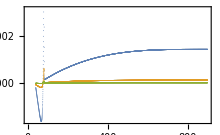

```mathematica
ExportAndShow["R(v) diff",ListPlot[Table[{VvecSkipped[[lastIndex;;]],RTables[RStarConstValues[[j+1]]][[lastIndex;;,-lastIndex+50*j]]-RTables[RStarConstValues[[j+2]]][[lastIndex;;,-lastIndex+50*(j+1)]]}//Transpose,{j,0,Length[RStarConstValues]-2}],Frame->True,FrameLabel->{MaTeX@"v"},PlotLegends->Placed[Table[MaTeX["R[T_0="<>ToString[RStarConstValues[[j+1]]]<>"]-R[T_0="<>ToString[RStarConstValues[[j+2]]]<>"]"],{j,0,Length[RStarConstValues]-2}],Right],ImageSize->TheImageSize]]
```

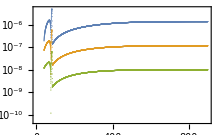

```mathematica
ExportAndShow["R(v) diff log",ListLogPlot[Table[{VvecSkipped[[lastIndex;;]],(RTables[RStarConstValues[[j+1]]][[lastIndex;;,-lastIndex+50*j]]-RTables[RStarConstValues[[j+2]]][[lastIndex;;,-lastIndex+50*(j+1)]])//Abs}//Transpose,{j,0,Length[RStarConstValues]-2}],Frame->True,FrameLabel->{MaTeX@"v"},PlotLegends->Placed[Table[MaTeX["R[T_0="<>ToString[RStarConstValues[[j+1]]]<>"]-R[T_0="<>ToString[RStarConstValues[[j+2]]]<>"]"],{j,0,Length[RStarConstValues]-2}],Right],ImageSize->TheImageSize]]
```

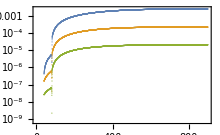

```mathematica
ExportAndShow["S(v) diff log",ListLogPlot[Table[{VvecSkipped[[lastIndex;;]],(STables[RStarConstValues[[j+1]]][[lastIndex;;,-lastIndex+50*j]]-STables[RStarConstValues[[j+2]]][[lastIndex;;,-lastIndex+50*(j+1)]])//Abs}//Transpose,{j,0,Length[RStarConstValues]-2}],Frame->True,FrameLabel->{MaTeX@"v"},PlotLegends->Placed[Table[MaTeX["S[T_0="<>ToString[RStarConstValues[[j+1]]]<>"]-S[T_0="<>ToString[RStarConstValues[[j+2]]]<>"]"],{j,0,Length[RStarConstValues]-2}],Right],ImageSize->TheImageSize]]
```

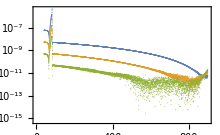

```mathematica
ExportAndShow["R,v(v) diff log",ListLogPlot[Table[{VvecSkipped[[lastIndex;;]][[2;;]],(RvTables[RStarConstValues[[j+1]]][[lastIndex;;,-lastIndex+50*j]]-RvTables[RStarConstValues[[j+2]]][[lastIndex;;,-lastIndex+50*(j+1)]])[[2;;]]//Abs}//Transpose,{j,0,Length[RStarConstValues]-2}],Frame->True,FrameLabel->{MaTeX@"v"},PlotLegends->Placed[Table[MaTeX["R_{,v}[T_0="<>ToString[RStarConstValues[[j+1]]]<>"]-R_{,v}[T_0="<>ToString[RStarConstValues[[j+2]]]<>"]"],{j,0,Length[RStarConstValues]-2}],Right],ImageSize->TheImageSize]]
```

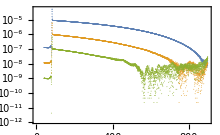

```mathematica
ExportAndShow["S,v(v) diff log",ListLogPlot[Table[{VvecSkipped[[lastIndex;;]][[2;;]],(SvTables[RStarConstValues[[j+1]]][[lastIndex;;,-lastIndex+50*j]]-SvTables[RStarConstValues[[j+2]]][[lastIndex;;,-lastIndex+50*(j+1)]])[[2;;]]//Abs}//Transpose,{j,0,Length[RStarConstValues]-2}],Frame->True,FrameLabel->{MaTeX@"v"},PlotLegends->Placed[Table[MaTeX["S_{,v}[T_0="<>ToString[RStarConstValues[[j+1]]]<>"]-S_{,v}[T_0="<>ToString[RStarConstValues[[j+2]]]<>"]"],{j,0,Length[RStarConstValues]-2}],Right],ImageSize->TheImageSize]]
```

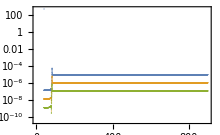

```mathematica
ExportAndShow["S,u(v) diff log",ListLogPlot[Table[{VvecSkipped[[lastIndex;;]],(SuTables[RStarConstValues[[j+1]]][[lastIndex;;,-lastIndex+50*j]]-SuTables[RStarConstValues[[j+2]]][[lastIndex;;,-lastIndex+50*(j+1)]])//Abs}//Transpose,{j,0,Length[RStarConstValues]-2}],Frame->True,FrameLabel->{MaTeX@"v"},PlotLegends->Placed[Table[MaTeX["S_{,u}[T_0="<>ToString[RStarConstValues[[j+1]]]<>"]-S_{,u}[T_0="<>ToString[RStarConstValues[[j+2]]]<>"]"],{j,0,Length[RStarConstValues]-2}],Right],ImageSize->TheImageSize]]
```

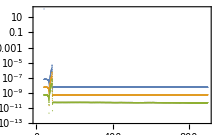

```mathematica
ExportAndShow["R,u(v) diff log",ListLogPlot[Table[{VvecSkipped[[lastIndex;;]],(RuTables[RStarConstValues[[j+1]]][[lastIndex;;,-lastIndex+50*j]]-RuTables[RStarConstValues[[j+2]]][[lastIndex;;,-lastIndex+50*(j+1)]])//Abs}//Transpose,{j,0,Length[RStarConstValues]-2}],Frame->True,FrameLabel->{MaTeX@"v"},PlotLegends->Placed[Table[MaTeX["R_{,u}[T_0="<>ToString[RStarConstValues[[j+1]]]<>"]-R_{,u}[T_0="<>ToString[RStarConstValues[[j+2]]]<>"]"],{j,0,Length[RStarConstValues]-2}],Right],ImageSize->TheImageSize]]
```